```mathematica
"definição do circulo"
a=1
```

definição do circulo

1

```mathematica
"definição da autofunção"
n=2
m=1
α = N[BesselJZero[n,m]]
ϕ1[r_,θ_]=1/a √(2/π)1/BesselJ[n+1,α] BesselJ[n,α*r/a]Cos[n*θ]
ϕ2[r_,θ_]=1/a √(2/π)1/BesselJ[n+1,α] BesselJ[n,α*r/a]Sin[n*θ]
```

definição da autofunção

2

1

5.13562

2.34901 BesselJ[2,5.13562 r] Cos[2 θ]

2.34901 BesselJ[2,5.13562 r] Sin[2 θ]

5.52008

-2.34489 BesselJ[0,5.52008 r]

0.

```mathematica
"esboço da autofunção com cosseno"
Plot3D[ϕ1[√(x^2 + y^2),ArcTan[y/x]],{x,-a,a},{y,-a,a},RegionFunction->Function[{x,y,z},x^2+y^2≤a^2]]
```

esboço da autofunção com cosseno

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

-Graphics3D-

curvas de nível da autofunção

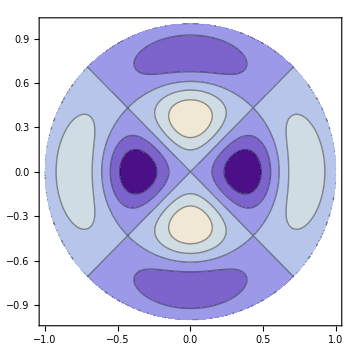

```mathematica
"curvas de nível da autofunção"
ContourPlot[ϕ1[√(x^2 + y^2),ArcTan[y/x]],{x,-a,a},{y,-a,a},RegionFunction->Function[{x,y,z},x^2+y^2≤a^2]]
```

```mathematica
"6 primeiras autofunções, respectivamente"
```

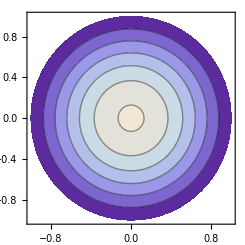
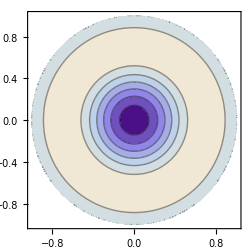
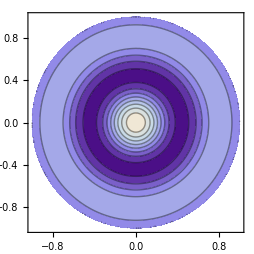

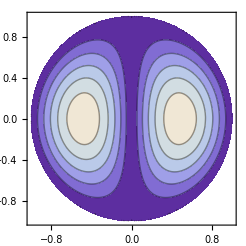
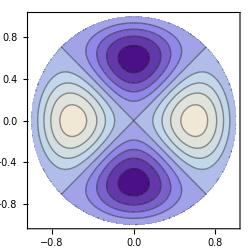
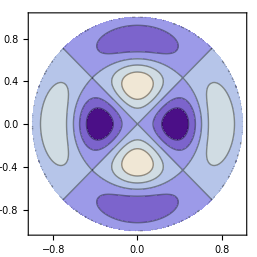

curvas nodais da autofunção

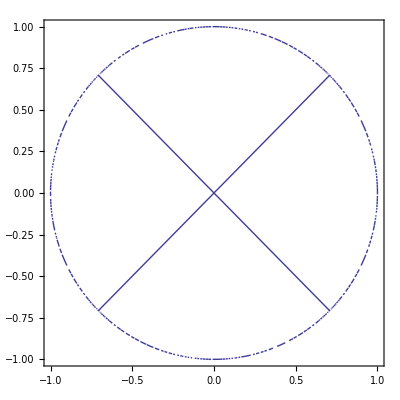

```mathematica
"curvas nodais da autofunção"
ContourPlot[ϕ1[√(x^2 + y^2),ArcTan[y/x]]== 0,{x,-a,a},{y,-a,a},RegionFunction->Function[{x,y,z},x^2+y^2≤a^2]]
```

```mathematica
"6 primeiras curvas nodais das autofunções, respectivamente"
```